```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,n_]:=LEFT[ω,δ,t,ϵ,n]=Module[{J=Inverse[β[ω,δ,1,0]],B:=Inverse[β[ω,δ,1,0]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,n];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ,50000].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ,50000].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

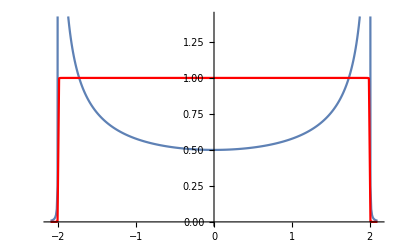

```mathematica
Monitor[Show[ListLinePlot[Table[{ω,-Im[IL[ω,0.001,1,0][[1,1]]]},{ω,Range[-2.1,2.1,0.01]}]],ListLinePlot[Table[{ω,tr[ω,0.001,1,0]},{ω,Range[-2.1,2.1,0.01]}],PlotRange->All,PlotStyle->Red]],ω]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
list[l_,s_]:=Join[Transpose[Join[{Range[1,s]},{RandomSample[Join[Table[0,s-l],Table[RandomInteger[{1,1}],l]]]}]]]
```

```mathematica
dist[l_,s_]:=dist[l,s]=Table[list[l,s],5000]
```

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,l_,s_,num_]:=Module[{Tin=T1[1],T=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[l,s][[num]][[ζ,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].ConjugateTranspose[Tin].J.Tin].Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[l,s][[num]][[ζ,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]],{ζ,s}];J=J];Il1=Inverse[IdentityMatrix[1]-sl1.T.SR[ω,δ,t,ϵ].T].sl1;
Ir1=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T.sl1.T].SR[ω,δ,t,ϵ];gdd1= Il1-ConjugateTranspose[Il1];grr1= Ir1-ConjugateTranspose[Ir1];Gnonlocal1= SR[ω,δ,t,ϵ].T.Il1;GNON1= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ],tr[ω,δ,t,ϵ],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/1DSIG.dat",Table[{ω,CAvg[ω,0.001,1,0,0.5,10,100,1]},{ω,Range[-2.1,2.1,0.01]}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/1DSIG.dat

```mathematica
transmission = Import["~/Downloads/mostimp/PhD_new/PhD/fwi/1D/CA_1D/*imp.dat"]
```

```mathematica
Dimensions[transmission]
```

{25,401,2}

```mathematica
input =Table[CAvg[ω,0.001,1,0,1,5,100,1],{ω,Range[-2,2,0.01]}]
```

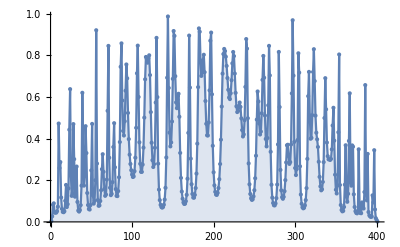

```mathematica
ListPlot[input,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
transmission[[2]][[101,2]]
```

0.510557

```mathematica
input[[1]]-transmission[[2]][[101,2]]
```

-0.0338633

```mathematica
Clear[d]
```

```mathematica
d:=d=Table[Table[input[[x]]-transmission[[a]][[201,2]],{a,2,24,4}],{x,1000}]
```

```mathematica
Dimensions[d]
```

{1000,6}

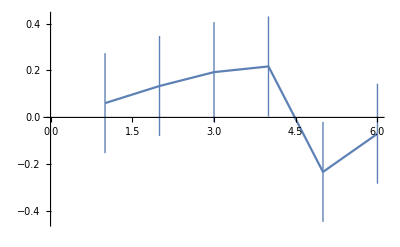

```mathematica
Table[Around[Table[d[[x]][[y]],{x,1000}]],{y,6}]//ListLinePlot
```

```mathematica
Transpose[Join[{Range[2,24,4]},{d[[301]]}]]
```

{{2,0.21873},{6,0.285147},{10,0.341041},{14,0.370156},{18,0.101329},{22,0.0808767}}

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/devi1.dat",Transpose[Join[{Range[2,24,4]},{d[[101]]}]]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/devi1.dat

```mathematica
Table[{4*y-2,Mean[Table[d[[x]][[y]],{x,401}]],StandardDeviation[Table[d[[x]][[y]],{x,401}]]},{y,6}]
```

{{2,0.200854,0.14338},{6,0.229599,0.16561},{10,0.256276,0.183588},{14,0.273567,0.194345},{18,0.263416,0.176354},{22,0.184833,0.131713}}

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/devi0.dat",%73]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/devi0.dat

```mathematica
Table[Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro"<>ToString[y]<>".dat",Table[d[[x]][[y]],{x,401}]],{y,6}]
```

{~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro1.dat,~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro2.dat,~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro3.dat,~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro4.dat,~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro5.dat,~/Desktop/Thesis/thesis26jun/Images/Chapter3/deviationerro6.dat}

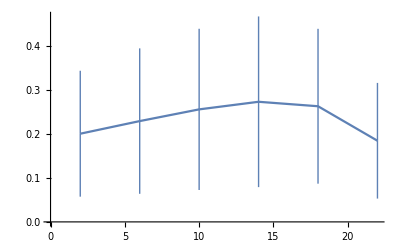

```mathematica
ListLinePlot[%39]
```

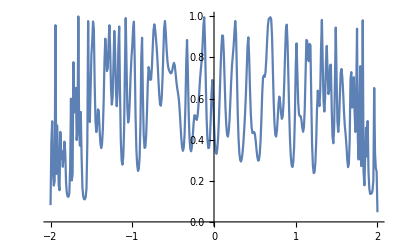

```mathematica
ListPlot[input,Joined->True]
```

```mathematica
Dimensions[transmission]
```

{25,401,2}

```mathematica
Monitor[Table[Table[{ω,Mean[ParallelTable[CAvg[ω,0.001,1,0,0.5,x,100,y],{y,3000}]]},{ω,Range[-2,2,0.01]}],{x,2,10,2}],{x,ω}]
```